```mathematica
n=15;
a=-1;
b=1;
xj[j_Integer]:=a+j (b-a)/n;
fj=Table[Random[Real,{-1,1}],{n+1}];
L[j_Integer,x_]:=(∏_(k=0)^(j-1) (x-xj[k])/(xj[j]-xj[k])) (∏_(k=j+1)^n (x-xj[k])/(xj[j]-xj[k]));
p[x_]:=∑_(j=0)^n fj[[j+1]] L[j,x];
p1=Plot[p[x],{x,a,b},DisplayFunction->Identity];
p2=ListPlot[Table[{xj[j-1],fj[[j]]},{j,1,n+1}],PlotStyle->{RGBColor[1,0,0],PointSize[0.01]},DisplayFunction->Identity];
Show[p1,p2,DisplayFunction->$DisplayFunction,Frame->True,PlotRange->Automatic]
```

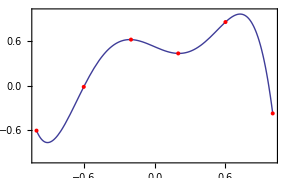
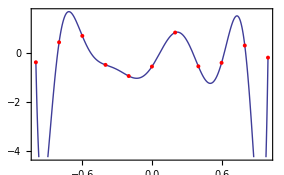
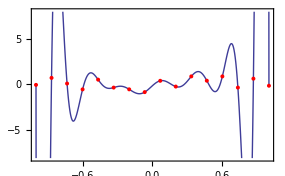
```mathematica
n=5                                      n=10                                     n=15
-Graphics--Graphics--Graphics-
```

```mathematica
n=5;
a=-1;
b=1;
xj[j_Integer]:=a+j (b-a)/n;
fj={-1,7,1,0,1,-3};
fj={-1,7,1,8,1,-3};
L[j_Integer,x_]:=(∏_(k=0)^(j-1) (x-xj[k])/(xj[j]-xj[k])) (∏_(k=j+1)^n (x-xj[k])/(xj[j]-xj[k]));
p[x_]:=∑_(j=0)^n fj[[j+1]] L[j,x];
p1=Plot[p[x],{x,a,b},DisplayFunction->Identity];
p2=ListPlot[Table[{xj[j-1],fj[[j]]},{j,1,n+1}],PlotStyle->{RGBColor[1,0,0],PointSize[0.02]},DisplayFunction->Identity];
Show[p1,p2,DisplayFunction->$DisplayFunction,Frame->True];
```

```mathematica
fj={-1,7,1,0,1,-3};                fj={-1,7,1,8,1,-3};
```